```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
nodes[order_,coords_]:=Block[{xa,xb,newcoords},
xa=coords[[1]];
xb=coords[[2]];
newcoords=Table[xa+(1-i)(xa-xb)/order,{i,1,order+1}];
newcoords
]
```

```mathematica
n
```

n

```mathematica
ComputeShape[order_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],x],{i,1,n}];
ListPoli[npoints]
]
```

```mathematica
phi=ComputeShape[1]
vecPtosPesos=GaussianQuadratureWeights[2,-1,1]
{xi,w}=Transpose[vecPtosPesos]
xx=0 phi[[1]]+ 1 phi[[2]]
J= D[xx,x]
integralxi=Sum[(phi[[1]]/.x->xi[[i]]) w[[i]],{i,1,Length[xi]}]
J integralxi
```

{1+1/2 (-1-x),(1+x)/2}

{{-0.57735,1.},{0.57735,1.}}

{{-0.57735,0.57735},{1.,1.}}

(1+x)/2

1/2

1.

0.5

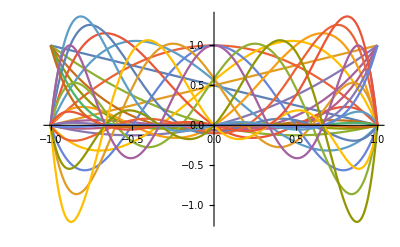

```mathematica
shape=Table[ComputeShape[order],{order,1,6}];
Plot[shape,{x,-1,1}]
```

```mathematica
ComputeData[xi_,coords_,order_]:=Block[{J,PHI,DPHI,x,xx,D2PHI},
PHI=ComputeShape[order];
DPHI=Table[D[PHI[[i]],x],{i,1,Length[PHI]}];
D2PHI=Table[D[DPHI[[i]],x],{i,1,Length[DPHI]}];
xx=Sum[PHI[[i]] coords[[i]],{i,1,Length[PHI]}];
J=D[xx,x];
{PHI,DPHI,D2PHI,J,xx}/.x->xi
]
```

```mathematica
ElementCalculations[order_,coords_,forcing_]:=Block[{Dphi,J,ip,vecPtosPesos,xi,w,Dpsi,D2psi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j},

vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
nnodes=Length[coords];
ek=Table[0,{nnodes},{nnodes}];
ef=Table[0,{nnodes}];
Dx=Table[0,{nnodes}];
For[ip=1,ip≤ Length[vecPtosPesos],ip++,
xi=vecPtosPesos[[ip,1]];
w=vecPtosPesos[[ip,2]];
{psi,Dpsi,D2psi,J,x}=ComputeData[xi,coords,order];
Dphi=Table[(1/J)Dpsi[[i]] ,{i,1,Length[Dpsi]}];
For[i=1,i≤Length[ek],i++,
ef[[i]]+= d (forcing)psi[[i]]   w J ;
For[j=1,j≤ Length[ek],j++,
ek[[i,j]]+= (a Dphi[[i]]Dphi[[j]]+b Dphi[[j]] psi[[i]] +c psi[[i]]  psi[[j]]) J  w;
];
];
];

{ek  ,ef }
]
```

```mathematica
Assemble[coords_,nels_,order_,forcing_]:=Block[{i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co},
sz=nels*order+1;
rows=order+1;
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
rowglob=1;
colglob=1;

For[k=1,k≤nels,k++,
co=nodes[order,{coords[[k]],coords[[k+1]]}];
{Ke,Fe}=ElementCalculations[order,co,forcing];
ik=(k-1)*order;
For[i=1,i≤rows,i++,
For[j=1,j≤cols,j++,
Kglob[[ik+i,ik+j]]+=Ke[[i,j]];
];
Fglob[[ik+i]]+=Fe[[i]];
];
];
{Kglob,Fglob}
]
```

```mathematica
ApplyBC[Kglob_,FGlob_,BCcond_]:=Block[{KG=Kglob,FG=FGlob,type1,val1,type2,val2,sz,BIGNUMBER=10^12},

sz=Length[KG];
{type1,val1,type2,val2}=BCcond;



If[type1==1,
(*Dirichlet - Specified Solution *)
KG[[1,1]]=BIGNUMBER;
FG[[1]]=val1 BIGNUMBER;
,
(*Newman - Specified Load*)
FG[[1]]+=val1;

];
If[type2==1,
(*Dirichlet - Specified Solution*)
KG[[sz,sz]]=BIGNUMBER;
FG[[sz]]=val2 BIGNUMBER;
,
(*Newman - Specified Load*)

FG[[sz]]+=val2;
];

{KG,FG}
]
```

```mathematica
ApplyBC[Kglob_,FGlob_,BCcond_]:=Block[{KG=Kglob,FG=FGlob,type1,val1,type2,val2,sz,BIGNUMBER=10^12},

sz=Length[KG];
{type1,val1,type2,val2}=BCcond;



If[type1==1,
(*Dirichlet - Specified Solution *)
KG[[1,1]]=BIGNUMBER;
FG[[1]]=val1 BIGNUMBER;
,
If[type1==2,
(*Newman - Specified Load*)
FG[[1]]+=val1;
,
(*Mixed - Specified Load*)
FG[[1]]+=val1[[2]];
KG[[1,1]]+=val1[[1]];
];

];
If[type2==1,
(*Dirichlet - Specified Solution *)
KG[[sz,sz]]=BIGNUMBER;
FG[[sz]]=val2 BIGNUMBER;
,
If[type2==2,
(*Newman - Specified Load*)
FG[[sz]]+=val2;
,
(*Mixed - Specified Load*)
FG[[sz]]+=val2[[2]];
KG[[sz,sz]]+=val2[[1]];
];

];

{KG,FG}
]
```

```mathematica
PostProcess[Kglob_,FGlob_,order_,coords_]:=Block[{Dphi,J,ip,vecPtosPesos,xi,w,Dpsi,D2psi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j},

vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
nnodes=Length[coords];
ek=Table[0,{nnodes},{nnodes}];
ef=Table[0,{nnodes}];
For[ip=1,ip≤ Length[vecPtosPesos],ip++,
xi=vecPtosPesos[[ip,1]];
w=vecPtosPesos[[ip,2]];
{psi,Dpsi,D2psi,J,x}=ComputeData[xi,coords,order];
Dphi=Table[(1/J)Dpsi[[i]] ,{i,1,Length[Dpsi]}];

];

]
```

```mathematica
Sol[nels_,order_,alpha_]:=Block[{k,i,phi,sol=0.},
For[k=1,k≤Length[alpha],k++,
phi=ComputeShape[order];

For[i=1,i≤Length[phi],i++,
sol+=phi[[i]] alpha[[k]] D[phi[[i]],x];
];
];
sol
]
```

```mathematica
ComputeSol[coords_,nels_,order_,alpha_]:=Block[{k,i,phi,sol=0.,xx,J,co,h,x},
phi=ComputeShape[order];
For[k=1,k≤nels,k++,
h=coords[[k]]-coords[[k+1]];
co=nodes[order,{coords[[k]],coords[[k+1]]}];
xx=Sum[phi[[i]] co[[i]],{i,1,Length[phi]}];
J=D[xx,x];
For[i=1,i≤Length[phi],i++,
sol+=phi[[i]] alpha[[k]] J;
];
];
sol
]
```

```mathematica
ComputeSol[nels_,order_,alpha_,coords_]:=Block[{dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x},
phi=ComputeShape[order];
sol=Table[0,{nels}];
dsol=Table[0,{nels}];
phisz=Length[phi];
For[i=1,i≤nels,i++,
xa=coords[[i]];
xb=coords[[i+1]];
For[j=1,j≤phisz,j++,
sol[[i]]+=(phi[[j]]/.{x->(2 x-(xa+xb))/(xb-xa)} )alpha[[j+k]];
dsol[[i]]+=D[(phi[[j]]/.{x->(2 x-(xa+xb))/(xb-xa)} ),x]alpha[[j+k]];
(*Print["j+k = ",j+k];
Print["j = ",j];*)
];
k+=phisz-1;
];
{sol,dsol}
]
```

```mathematica
ComputeError[coord_,Solution_,exactsol_]:=Block[{x,i,e,vecPtosPesos},
vecPtosPesos=GaussianQuadratureWeights[10,-1,1];
e=Table[0,{Length[vecPtosPesos]}];
For[i=1,i≤ Length[coord],i++,
e[[i]]={coord[[i]],(exactsol/.x->coord[[i]]) - Solution[[i]]};
];
Interpolation[e]
]
```

(14500. | -12500. | 0 | 0 | 0 | 0
-12500. | 25000. | -12500. | 0 | 0 | 0
0 | -12500. | 25000. | -12500. | 0 | 0
0 | 0 | -12500. | 25000. | -12500. | 0
0 | 0 | 0 | -12500. | 25000. | -12500.
0 | 0 | 0 | 0 | -12500. | 17500.)

(200000.
0.
0.
0.
0.
250000.)

{77.2727,73.6364,70.,66.3636,62.7273,59.0909}

{0,1.16415×10^-10,0,-1.16415×10^-10,0,-1.16415×10^-10}

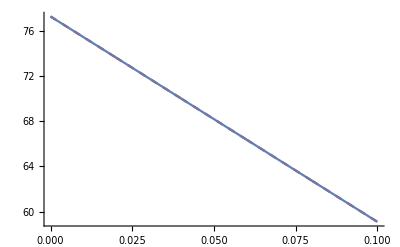

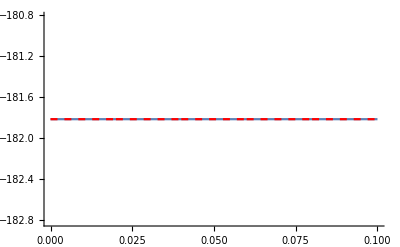

```mathematica
kk=250;
t1i=100;
t2i=50;
h1=2000;
h2=5000;
h=5;
p=1;
a=kk;
b=0;
c=0;
d=0;
xa=0;
xb=0.1;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}];
{k,f}=Assemble[coords,h,p,1];

{k,f}=ApplyBC[k,f,{3,{h1,h1 t1i},3,{ h2,h2 t2i}}];
k//MatrixForm
f//MatrixForm

n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"]
{sol,dsol}=ComputeSol[h,p,ceofs,coords];
tabsol=Table[Plot[sol[[i]],{x,coords[[i]],coords[[i+1]]},PlotStyle->{Red,Dashed}],{i,1,Length[coords]-1}];
tabdsol=Table[Plot[dsol[[i]],{x,coords[[i]],coords[[i+1]]},PlotStyle->{Red,Dashed}],{i,1,Length[coords]-1}];
k.ceofs-f//Chop
(*Print["Solution = ",ceofs//MatrixForm];*)
(*s=Sol[coords,h,p,ceofs];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
xalfa=Interpolation[tab,InterpolationOrder->1];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=t1i-(t1i-t2i)((x/kk)+ 1/h1)/(1/h1 + 1/h2 +(xb-xa)/kk);

errox[xx_]:=(Exata/.x->xx)-xalfa[xx];
dexata= D[Exata,x];
pldexata=Plot[dexata,{x,xa,xb},PlotRange->All];
pl=Plot[Exata,{x,xa,xb},PlotRange->All];
Show[tabsol,pl,PlotRange->All,AxesOrigin->{0,0}]
Show[pldexata,tabdsol,PlotRange->All,AxesOrigin->{0,0}]
```

(1000000000000 | -60. | 0 | 0 | 0 | 0
-60. | 120. | -60. | 0 | 0 | 0
0 | -60. | 120. | -60. | 0 | 0
0 | 0 | -60. | 120. | -60. | 0
0 | 0 | 0 | -60. | 120. | -60.
0 | 0 | 0 | 0 | -60. | 60.)

(100000000000000
48.
48.
48.
48.
-696.)

{0,0,0,0,0,0}

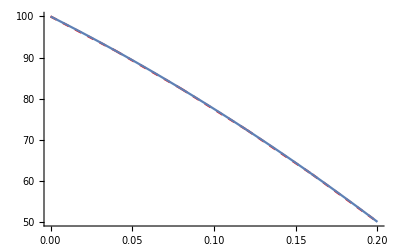

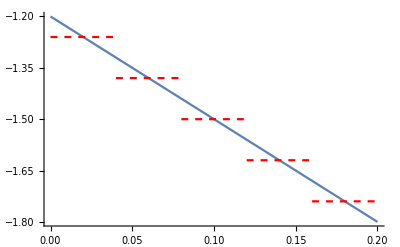

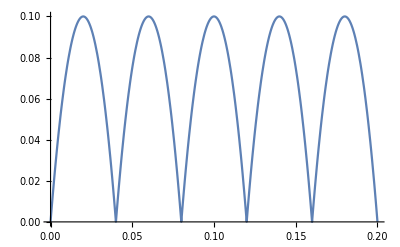

```mathematica
h=5;
p=1;
a=6000 0.4 10^-3;
b=0;
c=0;
d=3 10^6 0.4 10^-3;
xa=0;
xb=0.2;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}];
{k,f}=Assemble[coords,h,p,1];

{k,f}=ApplyBC[k,f,{1,100,2,-720}];
k//MatrixForm
f//MatrixForm

n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
{sol,dsol}=ComputeSol[h,p,ceofs,coords];
tabsol=Table[Plot[sol[[i]],{x,coords[[i]],coords[[i+1]]},PlotStyle->{Red,Dashed}],{i,1,Length[coords]-1}];
tabdsol=Table[Plot[6000 dsol[[i]]/10^6,{x,coords[[i]],coords[[i+1]]},PlotStyle->{Red,Dashed}],{i,1,Length[coords]-1}];
k.ceofs-f//Chop
(*Print["Solution = ",ceofs//MatrixForm];*)
(*s=Sol[coords,h,p,ceofs];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
xalfa=Interpolation[tab,InterpolationOrder->1];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=3 10^6/6000 (0.2 x-0.5 x^2)-1.8 10^6 x /6000 +100;

errox[xx_]:=(Exata/.x->xx)-xalfa[xx];
dexata=6000 D[Exata,x]/10^6;
pldexata=Plot[dexata,{x,xa,xb},PlotRange->All];
pl=Plot[Exata,{x,xa,xb},PlotRange->All];
Show[tabsol,pl,PlotRange->All,AxesOrigin->{0,0}]
Show[pldexata,tabdsol,PlotRange->All,AxesOrigin->{0,0}]
Plot[errox[x],{x,xa,xb}]
```

(1. | -1. | 0 | 0
-1. | 2. | -1. | 0
0 | -1. | 2. | -1.
0 | 0 | -1. | 1.)

(0.5
1.
1.
0.5)

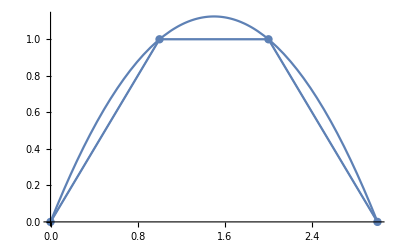

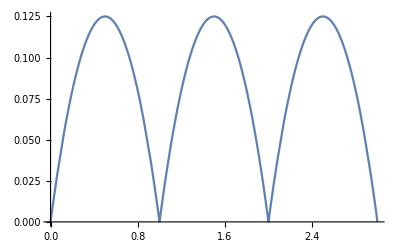

```mathematica
h=3;
p=1;
a=1;
b=0;
c=0;
d=1;
xa=0;
xb=3;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}];
{k,f}=Assemble[coords,h,p,1];
k//MatrixForm
f//MatrixForm
{k,f}=ApplyBC[k,f,{1,0,1,0}];
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];

{sol,dsol}=ComputeSol[h,p,ceofs,coords];
tabsol=Table[Plot[sol[[i]],{x,coords[[i]],coords[[i+1]]}],{i,1,Length[coords]-1}];
(*Print["Solution = ",ceofs//MatrixForm];*)
(*s=Sol[coords,h,p,ceofs];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
xalfa=Interpolation[tab,InterpolationOrder->1];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{-u''[x]-1==0,u[0]==0,u[3]==0},u[x],x][[1,1,2]];

errox[xx_]:=(Exata/.x->xx)-xalfa[xx];
pl=Plot[Exata,{x,xa,xb},PlotRange->All];
Show[tabsol,lp2,pl,PlotRange->All,AxesOrigin->{0,0}]
Plot[errox[x],{x,xa,xb}]
```

```mathematica
sol
```

{{1.×10^-12 (1-x)+1. x,1. (1+1/2 (2-2 x))+0.5 (-2+2 x),1. (1+1/2 (4-2 x))+5.×10^-13 (-4+2 x)},{1.,-2.22045×10^-16,-1.}}

(59.9333 | -65.8667 | 7.93333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-65.8667 | 139.733 | -65.8667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7.93333 | -65.8667 | 119.867 | -65.8667 | 7.93333 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -65.8667 | 139.733 | -65.8667 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 7.93333 | -65.8667 | 119.867 | -65.8667 | 7.93333 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -65.8667 | 139.733 | -65.8667 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 7.93333 | -65.8667 | 119.867 | -65.8667 | 7.93333 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -65.8667 | 139.733 | -65.8667 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 7.93333 | -65.8667 | 119.867 | -65.8667 | 7.93333
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -65.8667 | 139.733 | -65.8667
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.93333 | -65.8667 | 59.9333)

(8.
32.
16.
32.
16.
32.
16.
32.
16.
32.
8.)

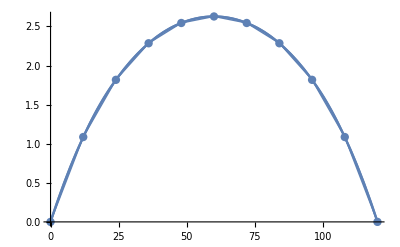

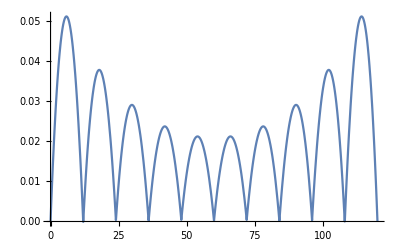

```mathematica
h=5;
p=2;
a=600;
b=0;
c=+0.5;
d=2;
xa=0;
xb=120;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}];
{k,f}=Assemble[coords,h,p,1];
k//MatrixForm
f//MatrixForm
{k,f}=ApplyBC[k,f,{1,0,1,0}];

n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
{sol,dsol}=ComputeSol[h,p,ceofs,coords];
tabsol=Table[Plot[sol[[i]],{x,coords[[i]],coords[[i+1]]}],{i,1,Length[coords]-1}];
(*Print["Solution = ",ceofs//MatrixForm];*)
(*s=Sol[coords,h,p,ceofs];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
xalfa=Interpolation[tab,InterpolationOrder->1];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{600u''[x]-0.5 u[x]+2==0,u[0]==0,u[120]==0},u[x],x][[1,1,2]];

errox[xx_]:=(Exata/.x->xx)-xalfa[xx];
pl=Plot[Exata,{x,xa,xb},PlotRange->All];
Show[tabsol,lp2,pl,PlotRange->All,AxesOrigin->{0,0}]
Plot[errox[x],{x,xa,xb}]
```

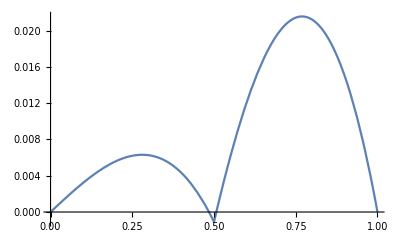
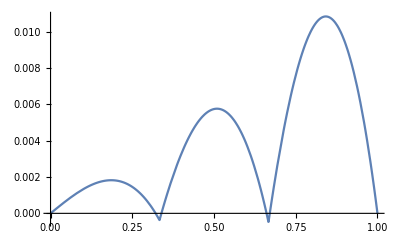
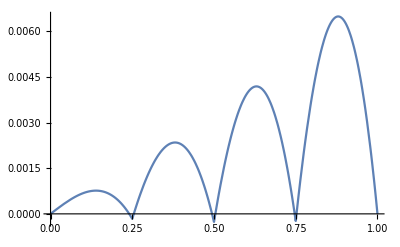
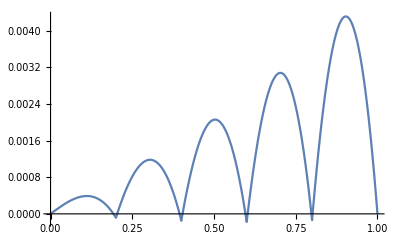
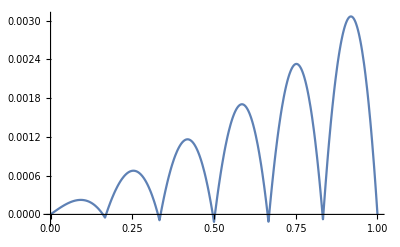

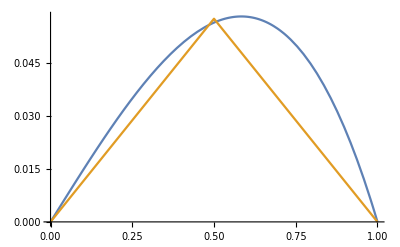
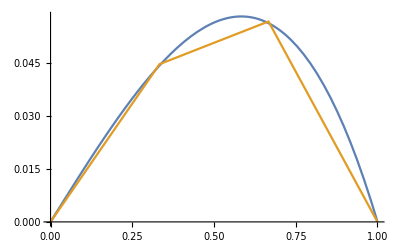
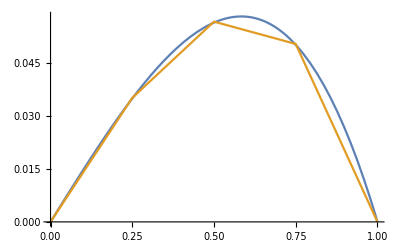

1.0179

0.505813

```mathematica
errovec={};
errovec2={};
errofuncs={};
For[i=2,i≤6,i++,
h=i;
p=1;
a=1;
b=0;
c=1;
d=1;
xa=0;
xb=1;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}];
{k,f}=Assemble[coords,h,p,x];
{k,f}=ApplyBC[k,f,{1,0,1,0}];
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
(*Print["Solution = ",ceofs//MatrixForm];*)
(*s=Sol[coords,h,p,ceofs];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
xalfa=Interpolation[tab,InterpolationOrder->1];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{-u''[x]+u[x]-x==0,u[0]==0,u[1]==0},u[x],x][[1,1,2]];

errox[xx_]:=(Exata/.x->xx)-xalfa[xx];
pl=Plot[Exata,{x,xa,xb},PlotRange->All];
Show[lp2,pl,PlotRange->All];
Plot[errox[x],{x,0,1}];
AppendTo[errovec,{Log[h]//N,-Log[Sqrt[NIntegrate[D[errox[x],x]^2+errox[x]^2,{x,xa,xb}]]]}];
AppendTo[errovec2,{Log[h]//N,-Log[Sqrt[NIntegrate[errox[x]^2,{x,xa,xb}]]]}];
AppendTo[errofuncs,xalfa];
];
Table[Plot[Exata-errofuncs[[i]][x],{x,xa,xb}],{i,1,Length[errofuncs]}]
Table[Plot[{Exata,errofuncs[[i]][x]},{x,xa,xb}],{i,1,Length[errofuncs]}]
ListLinePlot[{errovec,errovec2},AspectRatio->1.]
(Last[errovec][[1]]-First[errovec][[1]])/(Last[errovec][[2]]-First[errovec][[2]])
(Last[errovec2][[1]]-First[errovec2][[1]])/(Last[errovec2][[2]]-First[errovec2][[2]])
```

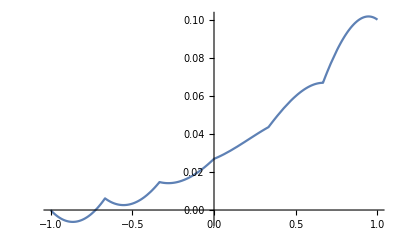
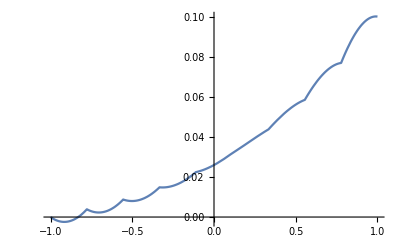
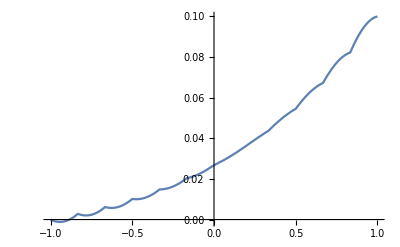
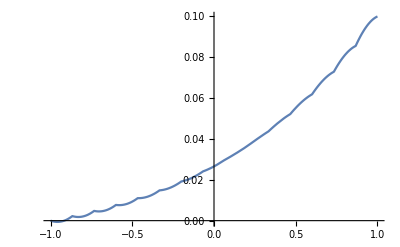
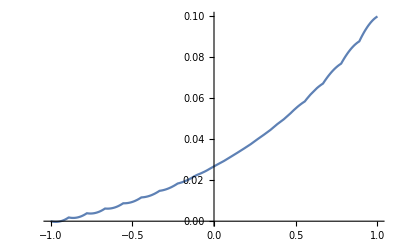

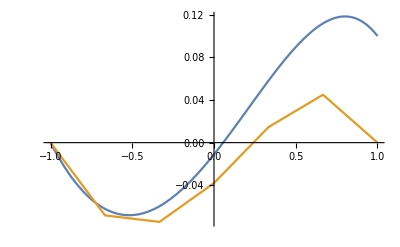
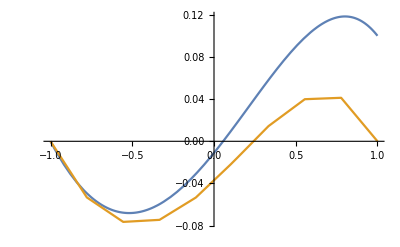
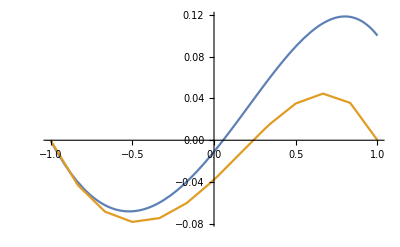

5.89734

17.6302

```mathematica
errovec={};
errovec2={};
errofuncs={};
For[i=2,i≤6,i++,
h=i;
p=3;
xa=-1;
xb=1.;
a=1;
b=1;
c=0;
d=1.;
Clear[coords];
Clear[ceofs];
coords=Table[delta,{delta,xa,xb,(xb-xa)/h}];
{k,f}=Assemble[coords,h,p,x];
{k,f}=ApplyBC[k,f,{1,0,1,0.1}];
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
xalfa=Interpolation[tab,InterpolationOrder->1];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{-u''[x]+u'[x]-x==0,u[-1]==0,u[1]==0.1},u[x],x][[1,1,2]];
pl=Plot[Exata,{x,xa,xb},PlotRange->All,PlotStyle->Red];
Show[lp2,pl,PlotRange->All];
Plot[errox[x],{x,0,1}];
AppendTo[errovec,{Log[h]//N,-Log[Sqrt[NIntegrate[D[errox[x],x]^2+errox[x]^2,{x,xa,xb}]]]}];
AppendTo[errovec2,{Log[h]//N,-Log[Sqrt[NIntegrate[errox[x]^2,{x,xa,xb}]]]}];
AppendTo[errofuncs,xalfa];
];
Table[Plot[Exata-errofuncs[[i]][x],{x,xa,xb}],{i,1,Length[errofuncs]}]
Table[Plot[{Exata,errofuncs[[i]][x]},{x,xa,xb}],{i,1,Length[errofuncs]}]
ListLinePlot[{errovec,errovec2},AspectRatio->1.]
(Last[errovec][[1]]-First[errovec][[1]])/(Last[errovec][[2]]-First[errovec][[2]])
(Last[errovec2][[1]]-First[errovec2][[1]])/(Last[errovec2][[2]]-First[errovec2][[2]])
```

{-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.}

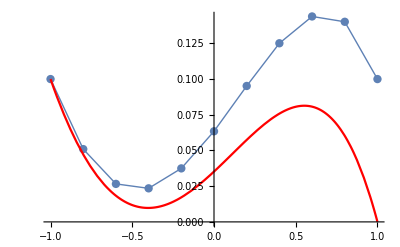

```mathematica
h=10;
p=1;
xa=-1;
xb=1.;
a=1;
b=1;
c=0;
d=1.;
Clear[coords];
Clear[ceofs];
coords=Table[delta,{delta,xa,xb,(xb-xa)/h}]
{k,f}=Assemble[coords,h,p,x];
{k,f}=ApplyBC[k,f,{1,0.1,1,0}];
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
xalfa=Interpolation[tab,InterpolationOrder->1];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{-u''[x]+u'[x]-x==0,u[-1]==0.1,u[1]==0},u[x],x][[1,1,2]];
pl=Plot[Exata,{x,xa,xb},PlotRange->All,PlotStyle->Red];
Show[lp2,pl,PlotRange->All]
```

{-1.,-0.6,-0.2,0.2,0.6,1.}

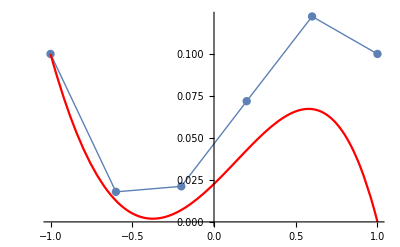

```mathematica
h=5;
p=1;
xa=-1;
xb=1.;
a=1;
b=1;
c=1;
d=1;
Clear[coords];
Clear[ceofs];
coords=Table[delta,{delta,xa,xb,(xb-xa)/h}]
{k,f}=Assemble[coords,h,p,x];
{k,f}=ApplyBC[k,f,{1,0.1,1,0}];
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{- u''[x]+ u'[x]+ u[x]-x==0,u[-1]==0.1,u[1]==0},u[x],x][[1,1,2]];
plex=Plot[Exata,{x,-1,1},PlotStyle->Red];
Show[lp2,plex,PlotRange->All]
```

{0,1/5,2/5,3/5,4/5,1}

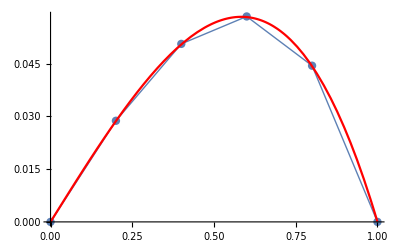

```mathematica
h=5;
p=1;
a=1;
b=0;
c=1;
d=1;
xa=0;
xb=1;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}]
{k,f}=Assemble[coords,h,p,x];
{k,f}=ApplyBC[k,f,{1,0,1,0}];
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
(*Print["Solution = ",ceofs//MatrixForm];*)
tab=Table[{(i-1)/n,ceofs[[i]]},{i,1,Length[ceofs]}];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{-u''[x]+u[x]-x==0,u[0]==0,u[1]==0},u[x],x][[1,1,2]];
plex=Plot[Exata,{x,0,1},PlotStyle->Red];
Show[lp2,plex]
```

{0.,0.314159,0.628319,0.942478,1.25664,1.5708}

1/2 x Sin[2 x]

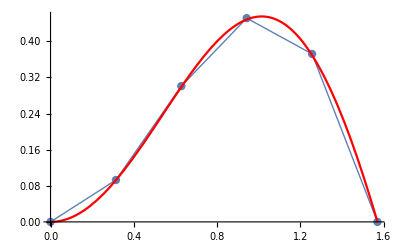

```mathematica
h=5;
p=1;
a=1;
b=0;
c=1;
d=1;
xa=0.;
xb=Pi/2;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}]
forcing=-2 Cos[x]^2+5 x Cos[x] Sin[x]+2 Sin[x]^2;
{k,f}=Assemble[coords,h,p,forcing];
val2=0.;
val1=val2;
{k,f}=ApplyBC[k,f,{1,val1,1,val2}];
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{-u''[x]+u[x]==forcing,u[xa]==val1,u[xb]==val2},u[x],x][[1,1,2]]
plex=Plot[Exata,{x,xa,xb},PlotStyle->Red];
Show[lp2,plex,PlotRange->All]
```

{0.,1.,2.,3.,4.,5.}

k = (1000000000000 | -4.725 | 1.35 | -0.325 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4.725 | 10.8 | -7.425 | 1.35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.35 | -7.425 | 10.8 | -4.725 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.325 | 1.35 | -4.725 | 7.4 | -4.725 | 1.35 | -0.325 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -4.725 | 10.8 | -7.425 | 1.35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.35 | -7.425 | 10.8 | -4.725 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.325 | 1.35 | -4.725 | 7.4 | -4.725 | 1.35 | -0.325 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -4.725 | 10.8 | -7.425 | 1.35 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.35 | -7.425 | 10.8 | -4.725 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.325 | 1.35 | -4.725 | 7.4 | -4.725 | 1.35 | -0.325 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.725 | 10.8 | -7.425 | 1.35 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.35 | -7.425 | 10.8 | -4.725 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.325 | 1.35 | -4.725 | 7.4 | -4.725 | 1.35 | -0.325
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.725 | 10.8 | -7.425 | 1.35
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.35 | -7.425 | 10.8 | -4.725
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.325 | 1.35 | -4.725 | 1000000000000)

f = (0
-0.00015
-0.00051
-0.000393333
-0.00069
-0.00087
-0.000593333
-0.00093
-0.00093
-0.000593333
-0.00087
-0.00069
-0.000393333
-0.00051
-0.00015
0)

-0.00416667 x+0.000333333 x^3-0.0000333333 x^4

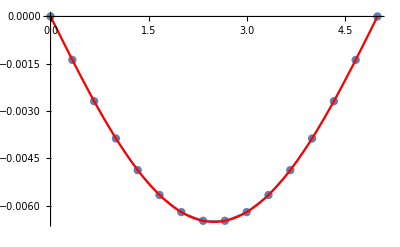

```mathematica
h=5;
p=3;
a=1;
b=0;
c=0;
d=1;
xa=0;
L=5.;
q=-8;
xb=L;
EI=10000;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}]
forcing=(-q x^2/2 + q L x/2)/EI;
{k,f}=Assemble[coords,h,p,forcing];
{k,f}=ApplyBC[k,f,{1,0,1,0}];
Print["k = ",k//MatrixForm]
Print["f = ",f//MatrixForm]
n=h  p;
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->Thick];
Exata=DSolve[{u''[x]==-forcing,u[0]==0,u[L]==0},u[x],x][[1,1,2]]
plex=Plot[Exata,{x,0,L},PlotStyle->Red];
Show[lp2,plex,PlotRange->All]
```

```mathematica
Clear[L]
p1=DSolve[{u''''[x]==0,u[0]==1,u'[0]==0,u[L]==0,u'[L]==0},u[x],x][[1,1,2]];
p2=DSolve[{u''''[x]==0,u[0]==0,u'[0]==1,u[L]==0,u'[L]==0},u[x],x][[1,1,2]];
p3=DSolve[{u''''[x]==0,u[0]==0,u'[0]==0,u[L]==1,u'[L]==0},u[x],x][[1,1,2]];
p4=DSolve[{u''''[x]==0,u[0]==0,u'[0]==0,u[L]==0,u'[L]==1},u[x],x][[1,1,2]];
phi={p1,p2,p3,p4}
shapes=Outer[Times,D[phi,x,x],D[phi,x,x]]
Clear[EI]
k=Table[EI Integrate[shapes[[i]],{x,0,L}],{i,1,Length[shapes]}]
k//MatrixForm
```

{(L^3-3 L x^2+2 x^3)/L^3,(L^2 x-2 L x^2+x^3)/L^2,(3 L x^2-2 x^3)/L^3,(-L x^2+x^3)/L^2}

{{(-6 L+12 x)^2/L^6,((-4 L+6 x) (-6 L+12 x))/L^5,((6 L-12 x) (-6 L+12 x))/L^6,((-2 L+6 x) (-6 L+12 x))/L^5},{((-4 L+6 x) (-6 L+12 x))/L^5,(-4 L+6 x)^2/L^4,((6 L-12 x) (-4 L+6 x))/L^5,((-4 L+6 x) (-2 L+6 x))/L^4},{((6 L-12 x) (-6 L+12 x))/L^6,((6 L-12 x) (-4 L+6 x))/L^5,(6 L-12 x)^2/L^6,((6 L-12 x) (-2 L+6 x))/L^5},{((-2 L+6 x) (-6 L+12 x))/L^5,((-4 L+6 x) (-2 L+6 x))/L^4,((6 L-12 x) (-2 L+6 x))/L^5,(-2 L+6 x)^2/L^4}}

{{(12 EI)/L^3,(6 EI)/L^2,-(12 EI)/L^3,(6 EI)/L^2},{(6 EI)/L^2,(4 EI)/L,-(6 EI)/L^2,(2 EI)/L},{-(12 EI)/L^3,-(6 EI)/L^2,(12 EI)/L^3,-(6 EI)/L^2},{(6 EI)/L^2,(2 EI)/L,-(6 EI)/L^2,(4 EI)/L}}

((12 EI)/L^3 | (6 EI)/L^2 | -(12 EI)/L^3 | (6 EI)/L^2
(6 EI)/L^2 | (4 EI)/L | -(6 EI)/L^2 | (2 EI)/L
-(12 EI)/L^3 | -(6 EI)/L^2 | (12 EI)/L^3 | -(6 EI)/L^2
(6 EI)/L^2 | (2 EI)/L | -(6 EI)/L^2 | (4 EI)/L)

```mathematica
Clear[L]
L=6
p1=DSolve[{u''''[x]==0,u[0]==1,u'[0]==0,u[L]==0,u'[L]==0},u[x],x][[1,1,2]];
p2=DSolve[{u''''[x]==0,u[0]==0,u'[0]==1,u[L]==0,u'[L]==0},u[x],x][[1,1,2]];
p3=DSolve[{u''''[x]==0,u[0]==0,u'[0]==0,u[L]==1,u'[L]==0},u[x],x][[1,1,2]];
p4=DSolve[{u''''[x]==0,u[0]==0,u'[0]==0,u[L]==0,u'[L]==1},u[x],x][[1,1,2]];
phi={p1,p2,p3,p4}
shapes=Outer[Times,D[phi,x,x],D[phi,x,x]]
Clear[EI]
k=Table[EI Integrate[shapes[[i]],{x,0,L}],{i,1,Length[shapes]}]
k//MatrixForm
```

6

{1/108 (108-9 x^2+x^3),1/36 (36 x-12 x^2+x^3),1/108 (9 x^2-x^3),1/36 (-6 x^2+x^3)}

{{(-18+6 x)^2/11664,((-24+6 x) (-18+6 x))/3888,((18-6 x) (-18+6 x))/11664,((-18+6 x) (-12+6 x))/3888},{((-24+6 x) (-18+6 x))/3888,(-24+6 x)^2/1296,((18-6 x) (-24+6 x))/3888,((-24+6 x) (-12+6 x))/1296},{((18-6 x) (-18+6 x))/11664,((18-6 x) (-24+6 x))/3888,(18-6 x)^2/11664,((18-6 x) (-12+6 x))/3888},{((-18+6 x) (-12+6 x))/3888,((-24+6 x) (-12+6 x))/1296,((18-6 x) (-12+6 x))/3888,(-12+6 x)^2/1296}}

{{EI/18,EI/6,-EI/18,EI/6},{EI/6,(2 EI)/3,-EI/6,EI/3},{-EI/18,-EI/6,EI/18,-EI/6},{EI/6,EI/3,-EI/6,(2 EI)/3}}

(EI/18 | EI/6 | -EI/18 | EI/6
EI/6 | (2 EI)/3 | -EI/6 | EI/3
-EI/18 | -EI/6 | EI/18 | -EI/6
EI/6 | EI/3 | -EI/6 | (2 EI)/3)

(1000000000000 | -1.68×10^7 | 0 | 0 | 0
-1.68×10^7 | 3.36×10^7 | -1.68×10^7 | 0 | 0
0 | -1.68×10^7 | 3.36×10^7 | -1.68×10^7 | 0
0 | 0 | -1.68×10^7 | 3.36×10^7 | -1.68×10^7
0 | 0 | 0 | -1.68×10^7 | 1.68×10^7)

(0
0.25
0.25
0.25
0.125)

1.5873×10^-7 x-3.96825×10^-8 x^3

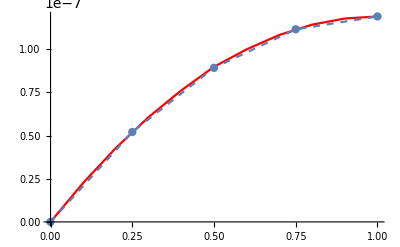

```mathematica
errovec={};
errovec2={};
errofuncs={};
Young = 2.1 10^8;
A=0.1 0.2;
h=4;
p=1;
a=Young A;
b=0;
c=0;
d=1;
xa=0;
xb=1;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}];
{k,f}=Assemble[coords,h,p,1];
{k,f}=ApplyBC[k,f,{1,0,2,0}];
k//MatrixForm
f//MatrixForm
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
n=h  p;
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->{Dashed}];
sftool={{1,1.190476 10^-7},{0.9,1.178571 10^-7},{0.8,1.142857 10^-7},{0.7,1.083333 10^-7},{0.6, 1 10^-7},{0.5, 8.98571 10^-8},{0.4,7.619047 10^-8},{0.3, 6.071428 10^-8},{0.2,4.285713 10^-8},{0.1,2.261904 10^-8},{0,0}};
plsftool=ListLinePlot[sftool,PlotStyle->{Red}];
Exata=DSolve[{-a u''[x]==x,u[0]==0,u[1]==1/(2 A Young)},u[x],x][[1,1,2]]
plex=Plot[Exata,{x,0,1},PlotStyle->Red];
(*plex=Plot[x^2/(2 Young A),{x,0,1},PlotStyle->Red];*)
Show[plsftool,lp2,PlotRange->All]
```

(1000000000000 | -1.68×10^7 | 0 | 0 | 0
-1.68×10^7 | 3.36×10^7 | -1.68×10^7 | 0 | 0
0 | -1.68×10^7 | 3.36×10^7 | -1.68×10^7 | 0
0 | 0 | -1.68×10^7 | 3.36×10^7 | -1.68×10^7
0 | 0 | 0 | -1.68×10^7 | 1.68×10^7)

(0
0.25
0.25
0.25
20.125)

1.5873×10^-7 x-3.96825×10^-8 x^3

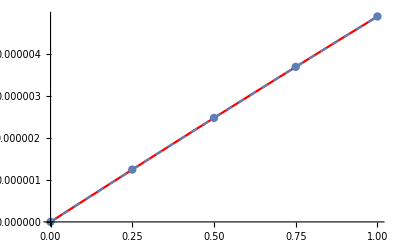

```mathematica
errovec={};
errovec2={};
errofuncs={};
Young = 2.1 10^8;
A=0.1 0.2;
h=4;
p=1;
a=Young A;
b=0;
c=0;
d=1;
xa=0;
xb=1;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}];
{k,f}=Assemble[coords,h,p,1];
{k,f}=ApplyBC[k,f,{1,0,2,20}];
k//MatrixForm
f//MatrixForm
(*ceofs=Inverse[k].f;*)
ceofs=LinearSolve[k,f,Method->"Banded"];
n=h  p;
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],ceofs[[i]]},{i,1,Length[ceofs]}];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->{Dashed}];
sftool={{1,4.880952 10^-6},{0.9,4.403571 10^-6},{0.8,3.923809 10^-6},{0.7,3.441666 10^-6},{0.6, 2.957143 10^-6},{0.5, 2.470238 10^-6},{0.4,1.980952 10^-6},{0.3, 1.489285 10^-6},{0.2,9.952379 10^-7},{0.1,4.988093 10^-7},{0,0}};
plsftool=ListLinePlot[sftool,PlotStyle->{Red}];
Exata=DSolve[{-a u''[x]==x,u[0]==0,u[1]==1/(2 A Young)},u[x],x][[1,1,2]]
plex=Plot[Exata,{x,0,1},PlotStyle->Red];
(*plex=Plot[x^2/(2 Young A),{x,0,1},PlotStyle->Red];*)
Show[plsftool,lp2,PlotRange->All]
```

```mathematica
0.5 0.5 20
```

5.

```mathematica
a
```

4.2×10^6

```mathematica
0.25 28 10^6
```

7.×10^6

# -Graphics- -Graphics-

# -Graphics-

```mathematica
0.25 20
```

5.

(0.375 | -0.375 | 0.
-0.375 | 1. | -0.625
0. | -0.625 | 35714.3)

(9.16667
12.5
0)

{2.11113×10^-6,1.23812×10^-6,2.1667×10^-11}

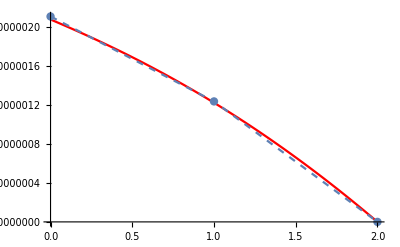

```mathematica
errovec={};
errovec2={};
errofuncs={};
Young = 28. 10^6 (*KN/m2*);
A=1/4(1+x);
h=2;
p=1;
a=Young A;
b=0;
c=0;
d=1;
xa=0;
xb=2;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}];
forcing=6.25(1+x);
{k,f}=Assemble[coords,h,p,forcing];
{k,f}=ApplyBC[k,f,{2,5,1,0}];
(k/Young)//MatrixForm
f//MatrixForm
sol=LinearSolve[k,f,Method->"Banded"]
n=h  p;
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],sol[[i]]},{i,1,Length[sol]}];
exact=1/Young (56.25 - 6.25 (1+x)^2 - 7.5 Log[(1+x)/3]);
plexact=Plot[exact,{x,0,2},PlotStyle->Red];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->{Dashed}];
Show[plexact,lp2,PlotRange->All]
```

```mathematica
exact/.x->1
```

1.22468×10^-6

```mathematica
errovec={};
errovec2={};
errofuncs={};
Young = 28. 10^6 (*KN/m2*);
A=1/4(1+x);
h=2;
p=1;
a=Young A;
b=0;
c=0;
d=1;
xa=0;
xb=2;
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}];
forcing=6.25(1+x);
{k,f}=Assemble[coords,h,p,forcing];
{k,f}=ApplyBC[k,f,{2,5,1,0}];
(k/Young)//MatrixForm
f//MatrixForm
sol=LinearSolve[k,f,Method->"Banded"]
n=h  p;
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],sol[[i]]},{i,1,Length[sol]}];
exact=1/Young (56.25 - 6.25 (1+x)^2 - 7.5 Log[(1+x)/3]);
plexact=Plot[exact,{x,0,2},PlotStyle->Red];
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->{Dashed}];
Show[plexact,lp2,PlotRange->All]
```

(0.375 | -0.375 | 0.
-0.375 | 1. | -0.625
0. | -0.625 | 35714.3)

(9.16667
12.5
0)

{2.11113×10^-6,1.23812×10^-6,2.1667×10^-11}

-Graphics-

```mathematica
Clear[a,b,c,d,L]
func[x_]:=a x^3+ b x^2+ c x +d
dfunc[x_]:=c+2 b x+3 a x^2
sol=Solve[{func[0]==0,dfunc[0]==0,func[L]==0,dfunc[L]==1},{a,b,c,d}]
(a x^3+ b x^2+ c x +d)/.sol
```

{{a→1/L^2,b→-1/L,c→0,d→0}}

{-x^2/L+x^3/L^2}

{{1/2-(3 x)/4+x^3/4},{1/4-x/4-x^2/4+x^3/4},{1/2+(3 x)/4-x^3/4},{-1/4-x/4+x^2/4+x^3/4}}

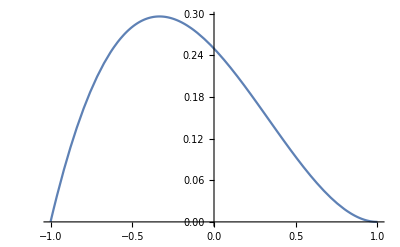

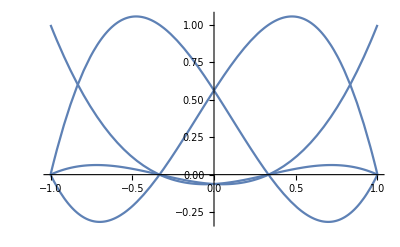

```mathematica
Clear[a,b,c,d]
func[x_]:=a x^3+ b x^2+ c x +d
dfunc[x_]:=c+2 b x+3 a x^2
sol=Solve[{func[-1]==1,dfunc[-1]==0,func[1]==0,dfunc[1]==0},{a,b,c,d}];
P1=(a x^3+ b x^2+ c x +d)/.sol;
sol=Solve[{func[-1]==0,dfunc[-1]==1,func[1]==0,dfunc[1]==0},{a,b,c,d}];
P2=(a x^3+ b x^2+ c x +d)/.sol;
sol=Solve[{func[-1]==0,dfunc[-1]==0,func[1]==1,dfunc[1]==0},{a,b,c,d}];
P3=(a x^3+ b x^2+ c x +d)/.sol;
sol=Solve[{func[-1]==0,dfunc[-1]==0,func[1]==0,dfunc[1]==1},{a,b,c,d}];
P4=(a x^3+ b x^2+ c x +d)/.sol;
phis={P1,P2,P3,P4}
Plot[phis[[2]],{x,-1,1}]
Plot[ComputeShape[3],{x,-1,1}]
```

```mathematica
ComputeData[xi_,coords_]:=Block[{J,PHI,DPHI,x,xx,D2PHI},
(*PHI=ComputeShape[order];*)
PHI={1/2-(3 x)/4+x^3/4,1/4-x/4-x^2/4+x^3/4,1/2+(3 x)/4-x^3/4,-1/4-x/4+x^2/4+x^3/4};
DPHI=Table[D[PHI[[i]],x],{i,1,Length[PHI]}];
D2PHI=Table[D[DPHI[[i]],x],{i,1,Length[DPHI]}];
xx=Sum[PHI[[j]] coords[[i]],{i,1,Length[coords]},{j,1,Length[PHI]}];
J=D[xx,x];
xx
]
```

{0,2,4,6}

4 (1/2+(3 x)/4-x^3/4)+2 (1/4-x/4-x^2/4+x^3/4)+6 (-1/4-x/4+x^2/4+x^3/4)

1+2 x+3 x^2

{0.,0.390625,0.625,0.796875,1.,1.32813,1.875,2.73438,4.}

{{-0.861136,0.347855},{-0.339981,0.652145},{0.339981,0.652145},{0.861136,0.347855}}

{1.,0.333333,1.,-0.333333}

{1.,0.333333,1.,-0.333333}

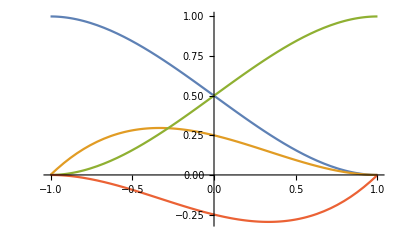

{1. (1+2 x+3 x^2),0.333333 (1+2 x+3 x^2),1. (1+2 x+3 x^2),-0.333333 (1+2 x+3 x^2)}

{3,3,3,-3}

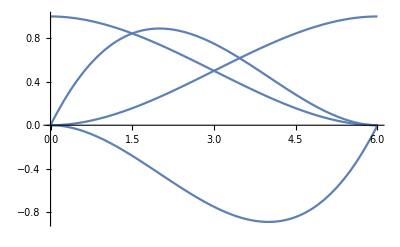

```mathematica
order=3;
shapes={1/2-(3 x)/4+x^3/4,1/4-x/4-x^2/4+x^3/4,1/2+(3 x)/4-x^3/4,-1/4-x/4+x^2/4+x^3/4};
nodess=nodes[order,{0,6}]
xx=Sum[shapes[[i]] nodess[[i]],{i,1,order+1}]
J=D[xx,x]//Simplify
Table[xx/.x->xi,{xi,-1,1,0.25}]
vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1]
{xi,w}=Transpose[vecPtosPesos];
integralxi=Table[Sum[(shapes[[j]]/.x->xi[[i]]) w[[i]],{i,1,Length[xi]}],{j,1,Length[shapes]}]
Table[Integrate[shapes[[j]],{x,-1.,1.}],{j,1,Length[shapes]}]
Plot[shapes,{x,-1,1}]
J integralxi 
phisdef={1/108 (108-9 x^2+x^3),1/36 (36 x-12 x^2+x^3),1/108 (9 x^2-x^3),1/36 (-6 x^2+x^3)};
Integrate[Table[phisdef[[i]],{i,1,Length[phisdef]}],{x,0,6}]
Plot[Table[phisdef[[i]],{i,1,Length[phisdef]}],{x,0,6}]
```

```mathematica
xx
```

4 (1/2+(3 x)/4-x^3/4)+2 (1/4-x/4-x^2/4+x^3/4)+6 (-1/4-x/4+x^2/4+x^3/4)

```mathematica
ComputeShape[order]
```

{1+(1+x) (-3/2+(9/8-9/16 (-1/3+x)) (1/3+x)),(1+x) (3/2+(-9/4+27/16 (-1/3+x)) (1/3+x)),(9/8-27/16 (-1/3+x)) (1/3+x) (1+x),9/16 (-1/3+x) (1/3+x) (1+x)}

{1+(1+x) (-3/2+(9/8-9/16 (-1/3+x)) (1/3+x)),(1+x) (3/2+(-9/4+27/16 (-1/3+x)) (1/3+x)),(9/8-27/16 (-1/3+x)) (1/3+x) (1+x),9/16 (-1/3+x) (1/3+x) (1+x)}

{0,2,4,6}

4 (9/8-27/16 (-1/3+x)) (1/3+x) (1+x)+27/8 (-1/3+x) (1/3+x) (1+x)+2 (1+x) (3/2+(-9/4+27/16 (-1/3+x)) (1/3+x))

3

{0.,0.75,1.5,2.25,3.,3.75,4.5,5.25,6.}

{{-0.861136,0.347855},{-0.339981,0.652145},{0.339981,0.652145},{0.861136,0.347855}}

{{-0.861136,-0.339981,0.339981,0.861136},{0.347855,0.652145,0.652145,0.347855}}

{0.25,0.75,0.75,0.25}

{0.25,0.75,0.75,0.25}

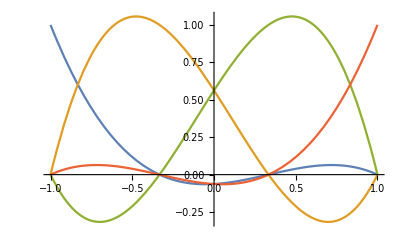

{0.75,2.25,2.25,0.75}

```mathematica
order=3;
shapes=ComputeShape[order]
nodess=nodes[order,{0,6}]
xx=Sum[shapes[[i]] nodess[[i]],{i,1,order+1}]
J=D[xx,x]//Simplify
Table[xx/.x->xi,{xi,-1,1,0.25}]
vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1]
{xi,w}=Transpose[vecPtosPesos]
integralxi=Table[Sum[(shapes[[j]]/.x->xi[[i]]) w[[i]],{i,1,Length[xi]}],{j,1,Length[shapes]}]
Table[Integrate[shapes[[j]],{x,-1.,1.}],{j,1,Length[shapes]}]
Plot[shapes,{x,-1,1}]
J integralxi
```

```mathematica
xx//Expand
```

3+3 x

```mathematica
shapes//Expand
```

{-1/16+x/16+(9 x^2)/16-(9 x^3)/16,9/16-(27 x)/16-(9 x^2)/16+(27 x^3)/16,9/16+(27 x)/16-(9 x^2)/16-(27 x^3)/16,-1/16-x/16+(9 x^2)/16+(9 x^3)/16}

```mathematica
shapes=ComputeShape[3]//Expand
0 shapes[[2]]+2shapes[[2]]+4shapes[[3]]+6shapes[[4]]//Expand
```

{-1/16+x/16+(9 x^2)/16-(9 x^3)/16,9/16-(27 x)/16-(9 x^2)/16+(27 x^3)/16,9/16+(27 x)/16-(9 x^2)/16-(27 x^3)/16,-1/16-x/16+(9 x^2)/16+(9 x^3)/16}

3+3 x

```mathematica
shapes={1/2-(3 x)/4+x^3/4,1/4-x/4-x^2/4+x^3/4,1/2+(3 x)/4-x^3/4,-1/4-x/4+x^2/4+x^3/4};
( 0 shapes[[1]]+2shapes[[2]]+4shapes[[3]]+6shapes[[4]])//Expand
```

1+x+x^2+x^3

{1+(-1+x/2) (1+x),(1-x) (1+x),1/2 x (1+x)}

{0,3,6}

3 (1-x) (1+x)+3 x (1+x)

3

{0.,0.75,1.5,2.25,3.,3.75,4.5,5.25,6.}

{{-0.774597,0.555556},{0.,0.888889},{0.774597,0.555556}}

{{-0.774597,0.,0.774597},{0.555556,0.888889,0.555556}}

{0.333333,1.33333,0.333333}

{0.333333,1.33333,0.333333}

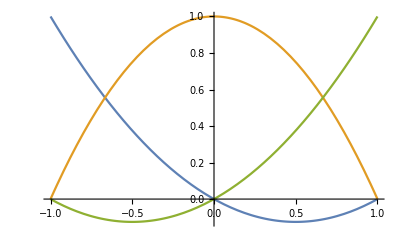

{1.,4.,1.}

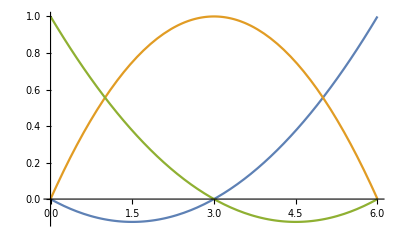

1

4

1

```mathematica
order=2;
shapes=ComputeShape[order]
nodess=nodes[order,{0,6}]
xx=Sum[shapes[[i]] nodess[[i]],{i,1,order+1}]
J=D[xx,x]//Simplify
Table[xx/.x->xi,{xi,-1,1,0.25}]
vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1]
{xi,w}=Transpose[vecPtosPesos]
integralxi=Table[Sum[(shapes[[j]]/.x->xi[[i]]) w[[i]],{i,1,Length[xi]}],{j,1,Length[shapes]}]
Table[Integrate[shapes[[j]],{x,-1.,1.}],{j,1,Length[shapes]}]
Plot[shapes,{x,-1,1}]
J integralxi 
Plot[{1/18(x-3)(x-0),-1/9(x-0)(x-6),1/18(x-3)(x-6)},{x,0,6}]
Integrate[1/18(x-3)(x-6),{x,0,6}]
Integrate[-1/9(x-0)(x-6),{x,0,6}]
Integrate[1/18(x-3)(x-0),{x,0,6}]
```

```mathematica
BeamMaterial[order_,coords_,forcing_]:=Block[{Dphi,J,ip,vecPtosPesos,xi,w,Dpsi,D2psi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,D2phi},

vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
nnodes=Length[coords];
ek=Table[0,{nnodes},{nnodes}];
ef=Table[0,{nnodes}];
Dx=Table[0,{nnodes}];
For[ip=1,ip≤ Length[vecPtosPesos],ip++,
xi=vecPtosPesos[[ip,1]];
w=vecPtosPesos[[ip,2]];
{psi,Dpsi,D2psi,J,x}=ComputeData[xi,coords,order];
Dphi=Table[(1/J)Dpsi[[i]] ,{i,1,Length[Dpsi]}];
D2phi=Table[(1/J)D2psi[[i]] ,{i,1,Length[D2psi]}];

For[i=1,i≤Length[ek],i++,
ef[[i]]+= d (forcing)psi[[i]]   w J ;
For[j=1,j≤ Length[ek],j++,
ek[[i,j]]+= (a D2psi[[i]]D2psi[[j]]) w J;
];
];
];

{ek  ,ef }
]
```

```mathematica
Assemble[coords_,nels_,order_,forcing_,Material_]:=Block[{i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co,jk},
sz=nels*order+1;
rows=order+1;
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
rowglob=1;
colglob=1;
For[k=1,k≤nels,k++,
co=nodes[order,{coords[[k]],coords[[k+1]]}];
{Ke,Fe}=Material[order,co,forcing];
(*Print["Ke = ",Ke//MatrixForm];
Print["Fe = ",Fe//MatrixForm];*)
ik=(k-1)*order;
For[i=1,i<=rows,i++,
jk=ik;
For[j=1,j<=cols,j++,
Kglob[[ik+i,jk+j]]+=Ke[[i,j]];
];
Fglob[[ik+i]]+=Fe[[i]];
];
];
{Kglob,Fglob}
]
```

# -Graphics-

{0,2}

{-6.66667×10^-13,-0.000040741,-0.0000760324,-0.000100948,-0.000111607,-0.0001057,-0.0000830078,-0.000045929,-1.19379×10^-12}

(1000000000000 | -4.4213×10^6 | 8.95342×10^6 | -1.22349×10^7 | 1.18923×10^7 | -8.03551×10^6 | 3.67178×10^6 | -1.06481×10^6 | 156302.
-4.4213×10^6 | 1.92234×10^7 | -4.09685×10^7 | 5.78455×10^7 | -5.79458×10^7 | 4.09183×10^7 | -1.99947×10^7 | 6.40794×10^6 | -1.06481×10^6
8.95342×10^6 | -4.09685×10^7 | 9.20305×10^7 | -1.36122×10^8 | 1.42778×10^8 | -1.06839×10^8 | 5.64914×10^7 | -1.99947×10^7 | 3.67178×10^6
-1.22349×10^7 | 5.78455×10^7 | -1.36122×10^8 | 2.12373×10^8 | -2.35694×10^8 | 1.8779×10^8 | -1.06839×10^8 | 4.09183×10^7 | -8.03551×10^6
1.18923×10^7 | -5.79458×10^7 | 1.42778×10^8 | -2.35694×10^8 | 2.7794×10^8 | -2.35694×10^8 | 1.42778×10^8 | -5.79458×10^7 | 1.18923×10^7
-8.03551×10^6 | 4.09183×10^7 | -1.06839×10^8 | 1.8779×10^8 | -2.35694×10^8 | 2.12373×10^8 | -1.36122×10^8 | 5.78455×10^7 | -1.22349×10^7
3.67178×10^6 | -1.99947×10^7 | 5.64914×10^7 | -1.06839×10^8 | 1.42778×10^8 | -1.36122×10^8 | 9.20305×10^7 | -4.09685×10^7 | 8.95342×10^6
-1.06481×10^6 | 6.40794×10^6 | -1.99947×10^7 | 4.09183×10^7 | -5.79458×10^7 | 5.78455×10^7 | -4.09685×10^7 | 1.92234×10^7 | -4.4213×10^6
156302. | -1.06481×10^6 | 3.67178×10^6 | -8.03551×10^6 | 1.18923×10^7 | -1.22349×10^7 | 8.95342×10^6 | -4.4213×10^6 | 1000000000000)

(0
-0.103845
0.0327337
-0.555344
0.320282
-0.925573
0.0982011
-0.726914
0)

{{0,-6.66667×10^-13},{1/4,-0.000040741},{1/2,-0.0000760324},{3/4,-0.000100948},{1,-0.000111607},{5/4,-0.0001057},{3/2,-0.0000830078},{7/4,-0.000045929},{2,-1.19379×10^-12}}

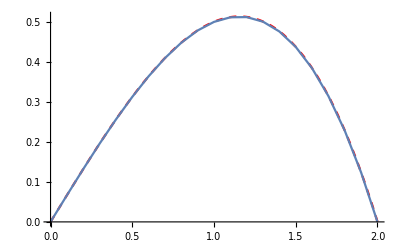

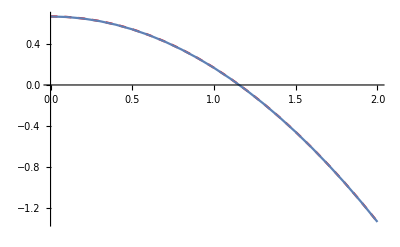

-0.000166786 x+0.0000595536 x^3-4.46429×10^-6 x^5

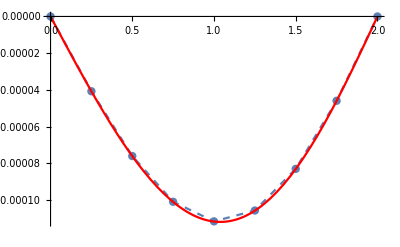

```mathematica
errovec={};
errovec2={};
errofuncs={};

e = 28 10^6(*KN/m2*);
i=0.1 0.2 0.2 0.2/12;
h=1;
p=8;
a=e i;
b=0;
c=0;
d=1;
xa=0;
xb=2;
q=x;
L=xb-xa;
forcing=-q;
 
coords=Table[xa+delta,{delta,0,xb,(xb-xa)/h}]

{k,f}=Assemble[coords,h,p,forcing,BeamMaterial];
{k,f}=ApplyBC[k,f,{1,0,1,0}];
sol=LinearSolve[k,f,Method->"Banded"]
k//MatrixForm
f//MatrixForm

n=h  p;
(*Print["Solution = ",ceofs//MatrixForm];*)
tab1=Table[delta,{delta,xa,xb,(xb-xa)/n}];
tab=Table[{tab1[[i]],sol[[i]]},{i,1,Length[sol]}]
lp2=ListLinePlot[tab,Mesh->All,PlotStyle->{Dashed}];
inercia=i;

xalfa=Interpolation[tab,InterpolationOrder->p];
d3sol=D[xalfa[x],x,x,x];
d2sol=D[xalfa[x],x,x];
tabM=Table[{xcoord,(d2sol/.x->xcoord) e i} ,{xcoord,xa,xb,0.1}];
tabQ=Table[{xcoord,(d3sol/.x->xcoord) e i} ,{xcoord,xa,xb,0.1}];
Q=D[0.667x-1/2x x x/3,x];
exactM=Plot[0.667x-1/2x x x/3,{x,xa,xb},PlotStyle->{Red,Dashed}];
exactQ=Plot[Q,{x,xa,xb},PlotStyle->{Red,Dashed}];
ApproxM=ListLinePlot[tabM];
ApproxQ=ListLinePlot[tabQ];
Show[exactM,ApproxM]
Show[exactQ,ApproxQ]

sol=DSolve[{e i u''[x]== 0.667x-1/2x x x/3,u[0]==0,u[L]==0},u[x],x][[1,1,2]]
exact=Plot[sol,{x,xa,xb},PlotStyle->Red];
Show[lp2,exact,PlotRange->All]
```